n$Si[lmb]

3.41696-2.09×10^7 lmb^2+1.48×10^17 lmb^4+0.013924/((-0.028+1.×10^12 lmb^2)^2)+0.138497/(-0.028+1.×10^12 lmb^2)

3.41696 - 2.09*^7*lmb^2 + 1.48*^17*lmb^4 + 0.013924/(-0.028 + 1.*^12*lmb^2)^2 + 0.138497/(-0.028 + 1.*^12*lmb^2)

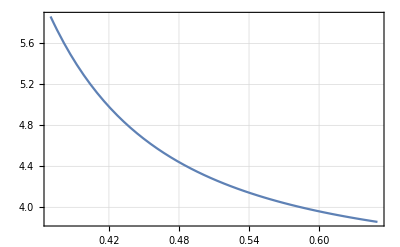

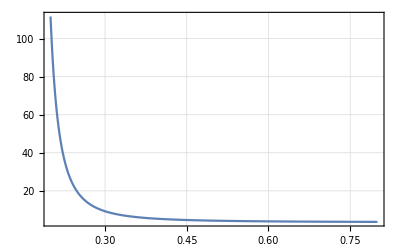

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ko$Si→3.17804×10^-23 (1.1888×10^20+1414.21 √(2.5747×10^32-6.43223×10^35 eps$Si)),lambda0$Si→-4.1992×10^-16 √(7.89546×10^17-7.07107 √(2.5747×10^32-6.43223×10^35 eps$Si))},{Ko$Si→3.17804×10^-23 (1.1888×10^20+1414.21 √(2.5747×10^32-6.43223×10^35 eps$Si)),lambda0$Si→4.1992×10^-16 √(7.89546×10^17-7.07107 √(2.5747×10^32-6.43223×10^35 eps$Si))},{Ko$Si→3.17804×10^-23 (1.1888×10^20-1414.21 √(2.5747×10^32-6.43223×10^35 eps$Si)),lambda0$Si→-1. √(1.39223×10^-13+1.24686×10^-30 √(2.5747×10^32-6.43223×10^35 eps$Si))},{Ko$Si→3.17804×10^-23 (1.1888×10^20-1414.21 √(2.5747×10^32-6.43223×10^35 eps$Si)),lambda0$Si→√(1.39223×10^-13+1.24686×10^-30 √(2.5747×10^32-6.43223×10^35 eps$Si))}}

xi$Si[lmb]

(4.40268×10^9 lmb^2)/(0.0001+(-0.121895+1.×10^12 lmb^2)^2)

(4.402681698765214*^9*lmb^2)/(0.0001 + (-0.12189462353667012 + 1.*^12*lmb^2)^2)

14645.7

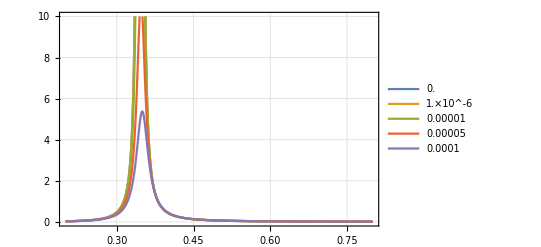

{0.0657613,0.0657694,0.0658433,0.0666629}

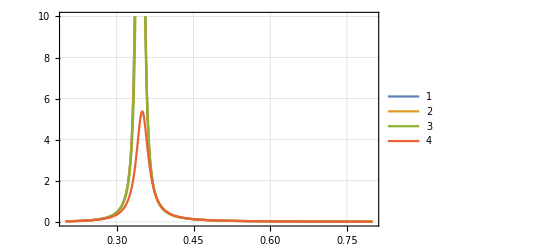

```mathematica
mkm = 10^-6;

L$Si[lambda_]:=1/((lambda / mkm)^2-0.028);
A$Si=3.41696;
B$Si=0.138497;
C1$Si=0.013924;
D1$Si=-0.0000209;
E1$Si=0.000000148;
n$Si[lambda_]:=A$Si+B$Si* L$Si[lambda]+C1$Si* L$Si[lambda]^2+D1$Si* (lambda / mkm)^2+E1$Si * (lambda / mkm)^4;
Print["n$Si[lmb]"];
nnn=N[n$Si[lmb]]
ToString[InputForm[nnn]]

Plot[n$Si[λ* mkm],{λ,0.37,0.65},PlotRange->All, Frame -> True, GridLines->Automatic]
Plot[n$Si[λ* mkm],{λ,0.2,0.8},PlotRange->All, Frame -> True, GridLines->Automatic]

lambda1$Si=0.3757 * mkm;
kappa1$Si=1.32;
lambda2$Si=0.589 * mkm;
kappa2$Si=0.030104;
xi$Si[lambda_, Ko_, lambda0_, eps_]:=Ko*(lambda / mkm)^2/(eps+((lambda / mkm)^2-(lambda0/ mkm)^2)^2);
sol$Si=Solve[{xi$Si[lambda1$Si, Ko$Si, lambda0$Si, eps$Si]==kappa1$Si,xi$Si[lambda2$Si, Ko$Si, lambda0$Si, eps$Si]==kappa2$Si},{Ko$Si,lambda0$Si}]

xi$Si[lambda_, epsValue_]:=((xi$Si[lambda, Ko$Si, lambda0$Si, eps$Si] /. sol$Si[[2]]) /. {eps$Si -> epsValue});
xi$Si[lambda_]:=xi$Si[lambda, 10^-4];

Print["xi$Si[lmb]"];
x=N[xi$Si[lmb]]
ToString[InputForm[x]]

N[xi$Si[0.345* mkm, 0]]

epsTbl=N[{0, 10^-6, 10^-5, 5 10^-5, 10^-4}];
xiTbl=Table[xi$Si[λ* mkm, epsTbl[[ii]]],{ii, Length[epsTbl]}];

Plot[xiTbl,{λ,0.2,0.8}, Frame->True, GridLines->Automatic, PlotRange->{0, 10}, PlotLegends->epsTbl]

{xi$Si[λ * mkm, 0], xi$Si[λ* mkm, 10^-6], xi$Si[λ* mkm, 10^-5], xi$Si[λ* mkm, 10^-4]} /. {λ -> 0.5}
Plot[{xi$Si[λ * mkm, 0], xi$Si[λ* mkm, 10^-6], xi$Si[λ* mkm, 10^-5], xi$Si[λ* mkm, 10^-4]},{λ,0.2,0.8}, Frame->True, GridLines->Automatic, PlotRange->{0, 10}, PlotLegends->Automatic]
```